```mathematica
alex[x4_,y4_,x_,y_]=(y4 (-1+2 x4+y4))/(3 x4 (x4-1))  x^3-x^2 y-x y^2+ (x4 (-1+2 y4+x4))/(3 y4 (y4-1)) y^3+(y4 (1-2 x4-y4))/(2 x4 (x4-1)) x^2+x y+(x4 (1-2 y4-x4))/(2 y4 (y4-1)) x^2
```

x y-x^2 y-x y^2+(x^2 x4 (1-x4-2 y4))/(2 (-1+y4) y4)+(x^2 (1-2 x4-y4) y4)/(2 (-1+x4) x4)+(x^3 y4 (-1+2 x4+y4))/(3 (-1+x4) x4)+(x4 y^3 (-1+x4+2 y4))/(3 (-1+y4) y4)

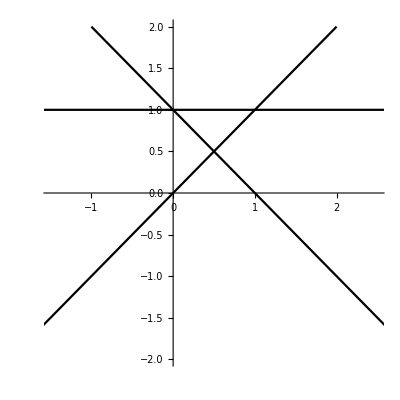

```mathematica
Graficas=Plot[{-x+1,x ,1},{x,-10,10},PlotRange->{{-1.5,2.5},{-2,2}},PlotStyle->Black,AspectRatio->1]
```

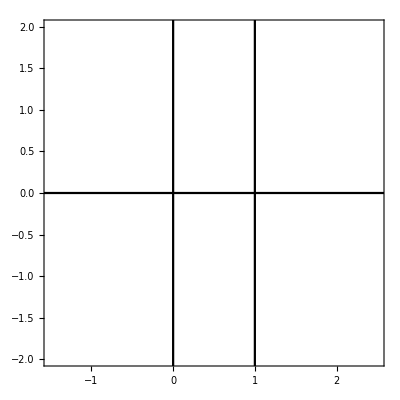

```mathematica
ejeReal=ContourPlot[{Im[x+I y]==0,Re[x+I y]==0,Re[x+I y]==1},{x,-10,10},{y,-10,10},PlotPoints->50,PlotRange->{{-1.5,2.5},{-2,2}},ContourStyle->Black,AspectRatio->1]
```

```mathematica
zeta[pt_]:=pt⟦1⟧+I pt⟦2⟧;
xy[z_]:={Re[z],Im[z]};
Manipulate[
Grid[{
{Show[ComplexListPlot[{{0},{1},{I},{Callout[zeta[pt],zeta[pt]]}},PlotStyle->{Directive[Red,PointSize[Large]],Directive[Green,PointSize[Large]],Directive[Blue,PointSize[Large]]}],Graficas,ejeReal,Graphics[{{Red,Line[{{1,0},xy[zeta[pt]]}]},{Green,Line[{{0,1},xy[zeta[pt]]}]}}],Axes->True,ImageSize->{375,375},PlotRange->{{-1,2},{-1.5,1.5}}],
Show[ContourPlot[alex[Re[zeta[pt]],Im[zeta[pt]],x,y],{x,-1,3/2},{y,-2,2},Contours->500,ImageSize->{375,375}]]
}
}],{{pt,{1/2,1/2}},Locator}]
```